## Animated Promo

```mathematica
cls=<|"Trigonometric Functions"-> RGBColor[Rational[212, 255], 0, Rational[4, 51]],"Constants & literals"-> RGBColor[Rational[133, 255], Rational[16, 51], Rational[31, 51]],"List Visualisation"-> RGBColor[Rational[253, 255], Rational[7, 17], Rational[1, 255]]|>;
```

```mathematica
data=<|"Trigonometric Functions"->{"ArcSin","ArcCos","ArcTan","ArcCsc","ArcSec","ArcCot","Cos","Sin","Tan","Csc","Sec","Cot","Sinc","Haversine"},"Constants & literals"->Select[vocabulary,StringContainsQ["$"]],
"String Operations"->{"StringJoin","StringLength","StringReverse","StringTake","StringDrop","StringInsert","StringReplacePart","StringPosition","StringCount","StringReplace","StringReplaceList","StringFreeQ","StringSplit","StringTrim"},
"List Visualisation"->Select[vocabulary,StringContainsQ[StartOfString~~"List"~~__~~"Plot"~~__]]
|>;
```

```mathematica
animatedPromo=Function[name,GraphicsRow[{
FeatureSpacePlot[vocabulary/.Map[#->Style[#,cls[name],PointSize[0.02]]&,data[name]],
FeatureExtractor->First@*embedding,
Method->"TSNE",
LabelingFunction->Tooltip,
PerformanceGoal->"Quality"
],
Dataset[<|name->#|>&/@data[name]][[1;;8]]},Alignment->Center,ImageSize->Full]]/@{"Trigonometric Functions","Constants & literals","List Visualisation"};
```

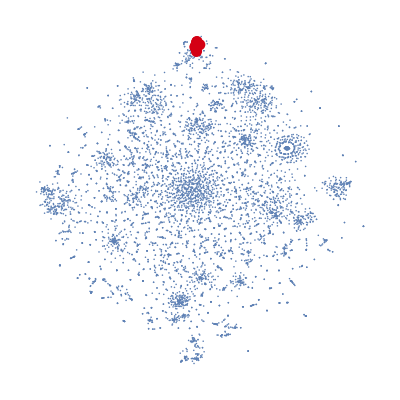

```mathematica
animatedPromo[[1]]
```

```mathematica
Export["promo.gif",animatedPromo,"GIF","AnimationRepetitions"->∞, "DisplayDurations"-> 0.8,ImageSize->800]
```

promo.gif

WolframAlphaQueryParseResults

RGBColor[Rational[253, 255], Rational[7, 17], Rational[1, 255]]

```mathematica
Function[name,Style[name, cls[name],18]]@"List Visualisation"
```

List Visualisation

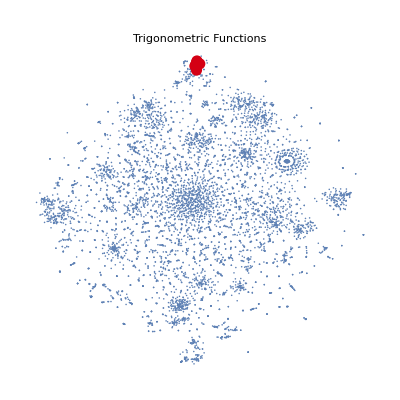
```mathematica
GraphicsRow[{-Graphics-,Dataset[<|"Functions"->#|>&/@data["Constants & literals"]][[1;;6]]},Alignment->Center
]
```

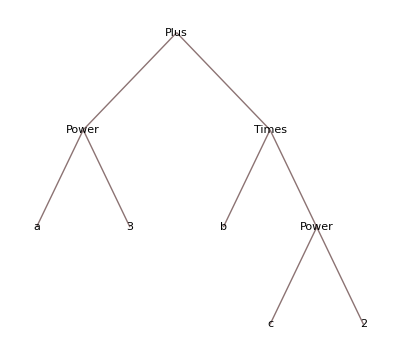

```mathematica
a^3+b c^2//TreeForm
```

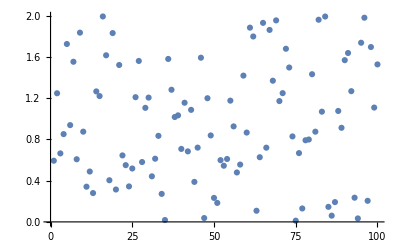

```mathematica
ListPlot[RandomReal[2,100],PlotMarkers->Automatic,Frame->None]
```

WolframAlphaQueryNoResults

```mathematica
RGBColor[Rational[212, 255], 0, Rational[4, 51]]//ToString
```

212     4
RGBColor[---, 0, --]
         255     51